```mathematica
l1=(l-1)(l+2);
l2=l(l+1);
df[f_,r_]:=f''[r]-l1(2r f'[r]+(r^2-l2)f[r])/(r^2(r^2-l1))+f[r];
```

```mathematica
findf[l0_, {A_,B_},eps_]:=Module[{fn,r0},
fn[r_]:=df[f,r]/.l->l0;
r0=√l1/.l->l0;
f[r]/.First@NDSolve[{fn[r]==0,f[r0+eps]==A,f''[r0+eps]==2B},f[r],{r,0.5r0,4.5r0}]
];
plotf13[f_,l0_]:=Plot[l1(f-r D[f,x]/.x->r)/(r^2-l1)/.l->l0,{r,0.5 √l1,4.5 √l1}/.l->l0];
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

InterpolatingFunction[{{2.64575, 23.8118}}, <>][r]

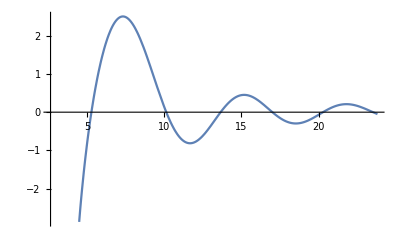

```mathematica
findf[5,{0,1}, 0.00000001]
plotf13[%,5]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

InterpolatingFunction[{{2.64575, 23.8118}}, <>][r]

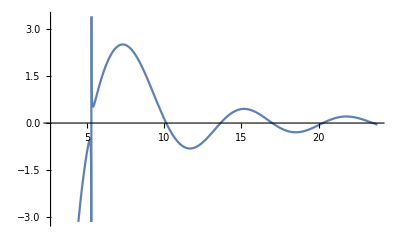

```mathematica
findf[5,{0.01,1}, 0.00000001]
plotf13[%,5]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

InterpolatingFunction[{{2.64575, 23.8118}}, <>][r]

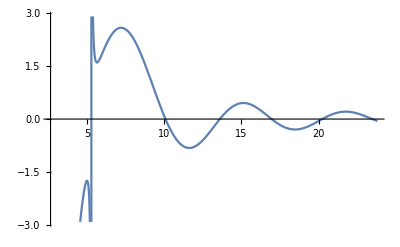

```mathematica
findf[5,{0.1,1}, 0.00000001]
plotf13[%,5]
```